```mathematica
$Assumptions={κ∈Reals,κ>0, g0>0,  g0∈Reals,ωp∈Reals,ω[x_]∈Reals,t∈Reals, τ∈Reals,μ∈Integers}
```

{κ∈ℝ,κ>0,g0>0,g0∈ℝ,ωp∈ℝ,ω[x_]∈ℝ,t∈ℝ,τ∈ℝ,μ∈ℤ}

```mathematica
validTriads[μ_]:=Select[Tuples[{1,2, 3},3],(#[[1]]-#[[2]]+#[[3]]==μ)&]
Do[Print["μ = ",μ," → ",validTriads[μ]],{μ,{1,2,3}}];
```

μ = 1 → {{1,1,1},{1,2,2},{1,3,3},{2,2,1},{2,3,2},{3,3,1}}

μ = 2 → {{1,1,2},{1,2,3},{2,1,1},{2,2,2},{2,3,3},{3,2,1},{3,3,2}}

μ = 3 → {{1,1,3},{2,1,2},{2,2,3},{3,1,1},{3,2,2},{3,3,3}}

```mathematica
eq[μ_]:=D[A[μ][t],t]==-(κ/2) A[μ][t]+
Sqrt[κe] S Exp[-I (ωp-ω[μ]) t] KroneckerDelta[μ,2]-
I g0 Sum[With[{α=triad[[1]],β=triad[[2]],γ=triad[[3]]},
A[α][t]  Conjugate[A[β][t]] A[γ][t] Exp[-I (ω[α]-ω[β]+ω[γ]-ω[μ]) t]
],
{triad,validTriads[μ]}
];
eqsystem = Table[eq[μ],{μ,{1,2,3}}]
```

{A[1]'[t]==-1/2 κ A[1][t]-ⅈ g0 (Conjugate[A[1][t]] (A[1][t])^2+2 Conjugate[A[2][t]] A[1][t] A[2][t]+ⅇ^(-ⅈ t (-ω[1]+2 ω[2]-ω[3])) Conjugate[A[3][t]] (A[2][t])^2+2 Conjugate[A[3][t]] A[1][t] A[3][t]),A[2]'[t]==ⅇ^(-ⅈ t (ωp-ω[2])) S √κe-1/2 κ A[2][t]-ⅈ g0 (2 Conjugate[A[1][t]] A[1][t] A[2][t]+Conjugate[A[2][t]] (A[2][t])^2+2 ⅇ^(-ⅈ t (ω[1]-2 ω[2]+ω[3])) Conjugate[A[2][t]] A[1][t] A[3][t]+2 Conjugate[A[3][t]] A[2][t] A[3][t]),A[3]'[t]==-1/2 κ A[3][t]-ⅈ g0 (ⅇ^(-ⅈ t (-ω[1]+2 ω[2]-ω[3])) Conjugate[A[1][t]] (A[2][t])^2+2 Conjugate[A[1][t]] A[1][t] A[3][t]+2 Conjugate[A[2][t]] A[2][t] A[3][t]+Conjugate[A[3][t]] (A[3][t])^2)}

```mathematica
expr = eqsystem[[2]]
```

A[2]'[t]==ⅇ^(-ⅈ t (ωp-ω[2])) S √κe-1/2 κ A[2][t]-ⅈ g0 (2 Conjugate[A[1][t]] A[1][t] A[2][t]+Conjugate[A[2][t]] (A[2][t])^2+2 ⅇ^(-ⅈ t (ω[1]-2 ω[2]+ω[3])) Conjugate[A[2][t]] A[1][t] A[3][t]+2 Conjugate[A[3][t]] A[2][t] A[3][t])

```mathematica
exprSPM = A[2]'[t]==ⅇ^(-ⅈ t (ωp-ω[2])) S √κe-1/2 κ A[2][t]-ⅈ g0 (Conjugate[A[2][t]] (A[2][t])^2)
```

A[2]'[t]==ⅇ^(-ⅈ t (ωp-ω[2])) S √κe-1/2 κ A[2][t]-ⅈ g0 Conjugate[A[2][t]] (A[2][t])^2

```mathematica
rulesNormA = {A[x_][t]->Sqrt[κ/(2g0)]a[x][t] Exp[I (ω[x]-ωp) t]}
```

{A[x_][t]→(ⅇ^(ⅈ t (-ωp+ω[x])) √(κ/g0) a[x][t])/(√2)}

```mathematica
eq1 = exprSPM/.rulesNormA
```

A[2]'[t]==ⅇ^(-ⅈ t (ωp-ω[2])) S √κe-(ⅇ^(ⅈ t (-ωp+ω[2])) κ √(κ/g0) a[2][t])/(2 √2)-(ⅈ ⅇ^(-ⅈ Conjugate[t] (-Conjugate[ωp]+Conjugate[ω[2]])+2 ⅈ t (-ωp+ω[2])) κ Conjugate[√(κ/g0) a[2][t]] (a[2][t])^2)/(2 √2)

```mathematica
D[Sqrt[κ/(2g0)]a[2][t] Exp[I (ω[2]-ωp) t],t]//Simplify
```

(ⅇ^(ⅈ t (-ωp+ω[2])) √(κ/g0) (-ⅈ (ωp-ω[2]) a[2][t]+a[2]'[t]))/(√2)

```mathematica
expr = (ⅇ^(ⅈ t (-ωp+ω[2])) √(κ/g0) (-ⅈ (ωp-ω[2]) a[2][t]+a[2]'[t]))/(√2)==ⅇ^(-ⅈ t (ωp-ω[2])) S √κe-(ⅇ^(ⅈ t (-ωp+ω[2])) κ √(κ/g0) a[2][t])/(2 √2)-(ⅈ ⅇ^(-ⅈ Conjugate[t] (-Conjugate[ωp]+Conjugate[ω[2]])+2 ⅈ t (-ωp+ω[2])) κ Conjugate[√(κ/g0) a[2][t]] (a[2][t])^2)/(2 √2);
```

```mathematica
expr = expr/. t->(2 τ)/κ
```

(ⅇ^((2 ⅈ τ (-ωp+ω[2]))/κ) √(κ/g0) (-ⅈ (ωp-ω[2]) a[2][(2 τ)/κ]+a[2]'[(2 τ)/κ]))/(√2)==ⅇ^(-(2 ⅈ τ (ωp-ω[2]))/κ) S √κe-(ⅇ^((2 ⅈ τ (-ωp+ω[2]))/κ) κ √(κ/g0) a[2][(2 τ)/κ])/(2 √2)-(ⅈ ⅇ^(-(2 ⅈ Conjugate[τ] (-Conjugate[ωp]+Conjugate[ω[2]]))/Conjugate[κ]+(4 ⅈ τ (-ωp+ω[2]))/κ) κ Conjugate[√(κ/g0) a[2][(2 τ)/κ]] (a[2][(2 τ)/κ])^2)/(2 √2)

```mathematica
rulesTime={ a[n_][(2 τ)/κ]->a[n][τ],Derivative[1][a[n_]][(2 τ)/κ]->(κ/2) Derivative[1][a[n]][τ]};
expr= expr/.rulesTime//Simplify
```

4 S √κe-ⅈ √2 κ √(κ/g0) Conjugate[a[2][τ]] (a[2][τ])^2==√2 √(κ/g0) ((κ-2 ⅈ (ωp-ω[2])) a[2][τ]+κ a[2]'[τ])

```mathematica
expr = Solve[expr,Derivative[1][a[2]][τ]]//Simplify
```

{{a[2]'[τ]→(2 √2 S √((g0 κe)/κ)-(κ-2 ⅈ (ωp-ω[2])) a[2][τ]-ⅈ κ Conjugate[a[2][τ]] (a[2][τ])^2)/κ}}

```mathematica
expr = expr/.S->s*κ/Sqrt[(8*κe*g0/κ)]//Simplify
```

{{a[2]'[τ]→s-((κ-2 ⅈ (ωp-ω[2])) a[2][τ])/κ-ⅈ Conjugate[a[2][τ]] (a[2][τ])^2}}

```mathematica
expr = expr/.{(ωp-ω[2])->-(κ/2) Δ}//Simplify
```

{{a[2]'[τ]→s+(-1-ⅈ Δ) a[2][τ]-ⅈ Conjugate[a[2][τ]] (a[2][τ])^2}}

```mathematica
rhs=Derivative[1][a[2]][τ]/. First@First@%
```

s+(-1-ⅈ Δ) a[2][τ]-ⅈ Conjugate[a[2][τ]] (a[2][τ])^2

```mathematica
eq = rhs/.{a[2][τ]->q+ⅈ p, s->sq+ⅈ sp}//ComplexExpand//Simplify//ReIm//ComplexExpand//Simplify
```

{p^3-q+sq+p (q^2+Δ),-p-p^2 q-q^3+sp-q Δ}

```mathematica
eq = eq/.{sp->0,sq->1.75}
```

{1.75+p^3-q+p (q^2+Δ),-p-p^2 q-q^3-q Δ}

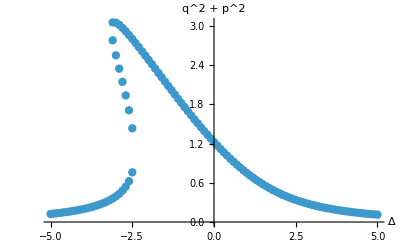

```mathematica
tab=Table[
{Δ->det,NSolve[(eq/.{Δ->det})==0,{q,p},Reals]},
{det,-5,5,.1}
];
format[row_]:=Module[
{det,quads},
{det,quads}=row;
Flatten[{det,#}]&/@quads
]
tab2=format/@tab;
points=Thread[{Δ/.tab2//Flatten,q^2+p^2/.tab2//Flatten}];
ListPlot[points, AxesLabel->{"Δ","q^2 + p^2"}, PlotStyle->PointSize[0.015]]
```